Computational homework 1 - Part 1- solution

question 1 :

first of all,we organize accessible data sets of 30 supernovas based on distance,velocity and velocity error:

```mathematica
distance={388.67525660474195,89.150517803079,397.343858810173,303.48659473244373,351.47045707046595,141.49175757474435,303.9420946507636,253.97625694088106,252.08532139625316,360.6448450019274,128.4062012555675,33.2104970140759,240.3110867334724,194.57287865829986,208.2485917227834,294.0341617962388,100.1090187675493,44.33374041923448,491.6932504809477,137.0963153994306,45.37766261333006,477.7517222075191,271.813174386292,487.52751246629606,151.96926210652265,28.363696886963076,463.9789505743887,41.96605206414735,245.8539571920331,284.122550340853};
```

```mathematica
velocity={29697.660733107186,6342.482075361154,28272.987088169837,20980.5490678462,25112.009372043118,10356.391521918325,22707.472579602276,19440.139404518835,19271.168332371253,26964.985437004605,9232.589081249618,2501.2473074050663,19155.308080717205,13018.635864567514,14874.013800384602,20961.37064076838,7477.266063081523,3331.559453325888,34521.075469474796,9933.954676792184,3212.1651474206556,34138.682414060444,19404.88908284509,34792.547597306395,11183.971070318434,2184.3416247448945,33580.35237927839,3035.3399324262273,16290.569489120782,20093.359992373724};
```

```mathematica
verror={1558.7562041068816,263.48896735881243,1486.232938447887,1075.269031058921,1381.3065190551806,651.7695775295131,1283.4730104604864,1116.3706083804445,1075.552541156502,1159.260586053102,461.3448890286077,115.8248021455144,1162.2496986638807,748.980953276404,787.866429036978,978.2002209947094,431.5674330925062,146.5183597014081,1585.3115577031767,410.33772804189056,123.72132572875307,1862.250772112024,1030.755704063533,1592.441238198762,645.590585131115,56.63609205402409,1294.5943816405681,199.85294911227476,772.9156418762402,938.0556613079968};
```

we should take into account that as a theoretical point of view, we know that the graph of velocity based on distance is a straight line which passes from the origin.so it would have only one free parameter:(A=χ^2 is the loss function)

```mathematica
A[H0_]:=Sum[((velocity[[i]]-(H0(distance[[i]])))/verror[[i]])^2,{i,1,30}]
```

```mathematica
Solve[D[A[H0],H0]==0,H0]
```

```mathematica
{{H0->72.66511324234139}}
```

{{H0→72.6651}}

in the following part, we want to calculate the amount of uncertainty of H0 :

```mathematica
Reduce[Sum[((velocity[[i]]-(H0+δh)(distance[[i]]))/verror[[i]])^2,{i,1,30}]-Sum[((velocity[[i]]-(H0(distance[[i]])))/verror[[i]])^2,{i,1,30}]==1,δh]/.H0->72.66511324234139//FullSimplify
```

```mathematica
δh==-0.6302131124299523||δh==0.6302131124299523
```

δh==-0.630213||δh==0.630213

H = 72.66511324234139 ± 0.6302131124299523

in order to plot the graph of the hubble constant, we define data which includes velocity and distance:

```mathematica
data={{388.67525660474195,29697.660733107186},{89.150517803079,6342.482075361154},{397.343858810173,28272.987088169837},{303.48659473244373,20980.5490678462},{351.47045707046595,25112.009372043118},{141.49175757474435,10356.391521918325},{303.9420946507636,22707.472579602276},{253.97625694088106,19440.139404518835},{252.08532139625316,19271.168332371253},{360.6448450019274,26964.985437004605},{128.4062012555675,9232.589081249618},{33.2104970140759,2501.2473074050663},{240.3110867334724,19155.308080717205},{194.57287865829986,13018.635864567514},{208.2485917227834,14874.013800384602},{294.0341617962388,20961.37064076838},{100.1090187675493,7477.266063081523},{44.33374041923448,3331.559453325888},{491.6932504809477,34521.075469474796},{137.0963153994306,9933.954676792184},{45.37766261333006,3212.1651474206556},{477.7517222075191,34138.682414060444},{271.813174386292,19404.88908284509},{487.52751246629606,34792.547597306395},{151.96926210652265,11183.971070318434},{28.363696886963076,2184.3416247448945},{463.9789505743887,33580.35237927839},{41.96605206414735,3035.3399324262273},{245.8539571920331,16290.569489120782},{284.122550340853,20093.359992373724}};
```

```mathematica
Fit[data,{d},d]
```

72.2261 d

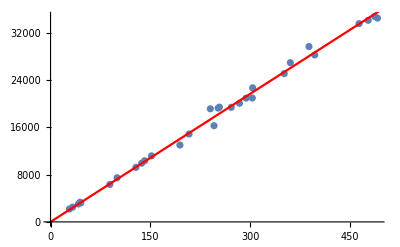

```mathematica
graph1=Show[{ListPlot[data],Plot[%,{d,0,500},PlotStyle->{Red}]}]
```

question 2 :

if we assumed that distance is a quadratic function of velocity,in this case it would have 2 free parameters: (p=χ^2 is the loss function)

```mathematica
p[H0_,H1_]:=Sum[((velocity[[i]]-(H0(distance[[i]])+H1 (distance[[i]])^2))/verror[[i]])^2,{i,1,30}]
```

```mathematica
eq1=D[p[H0,H1],H0]==0;
```

```mathematica
eq2=D[p[H0,H1],H1]==0;
```

```mathematica
Solve[{eq1,eq2},{H0,H1}]
```

{{H0→73.9742,H1→-0.00573579}}

```mathematica
{{H0->73.97415978868139,H1->-0.005735788502978752}}
```

{{H0→73.9742,H1→-0.00573579}}

in the following part, we want to calculate the amount of uncertainty of H0 :

```mathematica
Reduce[Sum[((velocity[[i]]-(H0+δh0)(distance[[i]])+H1(distance[[i]])^2)/verror[[i]])^2,{i,1,30}]-Sum[((velocity[[i]]-H0(distance[[i]])+H1(distance[[i]])^2)/verror[[i]])^2,{i,1,30}]==2.3,δh0]/.{H0->73.97415978868139,H1->-0.005735788502978752}//FullSimplify
```

```mathematica
δh0==-5.4051882016101525||δh0==0.1690020162501285
```

δh0==-5.40519||δh0==0.169002

```mathematica
Reduce[Sum[((velocity[[i]]-H0(distance[[i]])+(H1+δh1)(distance[[i]])^2)/verror[[i]])^2,{i,1,30}]-Sum[((velocity[[i]]-H0(distance[[i]])+H1(distance[[i]])^2)/verror[[i]])^2,{i,1,30}]==2.3,δh1]/.{H0->73.97415978868139,H1->-0.005735788502978752}//FullSimplify
```

```mathematica
δh1==-0.0005127975739367964||δh1==0.023455951585851825
```

δh1==-0.000512798||δh1==0.023456

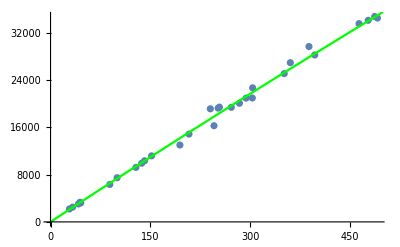

```mathematica
graph2=Show[{ListPlot[data],Plot[v=(H0)d+(H1)d^2/.{H0->73.97415978868139,H1->-0.005735788502978752},{d,0,500},PlotStyle->{Green}]}]
```

All of models in one graph :

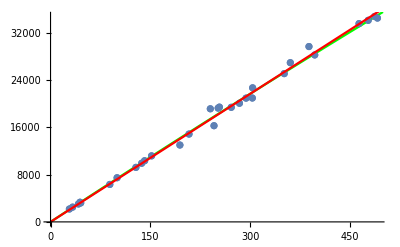

```mathematica
Show[{graph2,graph1}]
```

according to the uncertainty of quantities H,H0,H1 , it’s obvious that the first model which was linear equation is more appropriate for these data sets.